## CGS Astronomy Constants

Module by Ian Czekala and Josh Suresh, Harvard Astronomy 2010. Contact iczekala@cfa.harvard.edu with any corrections.

### Setup

Clear all defined variables

```mathematica
Clear["Global`*"]
```

Import package to label PlotLegends

```mathematica
Needs["PlotLegends`"]
```

Used like:

```mathematica
(*Plot[{Sin[x], Cos[x]}, {x, 0, 2Pi}, PlotLegend->{"sine", "cosine"}]*)
```

### Physics Constants

```mathematica
h=6.626068*^-27 (* cm^2 g s^-1 *);
=1.05457148*^-27 (* cm^2 g s^-1 *);
```

```mathematica
c=2.99792458*^10 (* cm s^-1 *);
```

Mass of elementary particles:

```mathematica
Me=9.10938*^-28 (*g*);
Mp=1.67262*^-24 (*g*);
Mn=1.674927*^-24 (*g*);
```

Mass of Hydrogen

```mathematica
MH = 1.6733*^-24 (*g*);
```

Atomic Mass Unit

```mathematica
amu = 1.6605402*^-24 (*g*);
```

Charge of electron

```mathematica
eC=4.80321*^-10 (* esu = √(erg cm) *);
```

Fine Structure constant

```mathematica
α=7.2973525376*^-3 (* unitless *);
```

Bohr Radius

```mathematica
a0=5.29177*^-9(* cm *);
```

Boltzmann constant

```mathematica
k=1.38065*^-16 (* cm^2 g s^-2 K^-1 *);
```

Stefan-Boltzman constant

```mathematica
σ = 5.670400*^-5 (* erg cm^-2 s^-1 K^-4*);
```

Rydberg constant

```mathematica
R = 2.1798741*^-11 (*erg*);
```

Gravitational constant

```mathematica
G=6.67259*10^-8 (* cm^3 g^-1 s^-2 *);
```

### Cosmology

```mathematica
Ho = 70 (*km/s/Mpc*);
```

```mathematica
c = 3.0*^5 (*km/s*);
```

```mathematica
Mpc = 3.09*^24 (*cm*);
```

```mathematica
HoU = Ho 10^5/Mpc(*cm/s/cm*);
```

### Astronomy Constants

Sun:

```mathematica
MS=1.98892*^33 (* g *);
RS=6.955*10^10 (* cm *);
LS=3.839*10^33 (* erg s^-1 *);
TS = 5777 (*k*);
```

Earth:

```mathematica
ME=5.9742*^27 (* g *);
RE=6.3781*^8 (* cm *);
```

Distance

```mathematica
AU = 1.49598*10^13(* cm *);
pc = 3.08568025*10^18 (* cm *);
kpc = 10^3 pc (*cm*);
Mpc = 10^6 pc (*cm*);
```

```mathematica
rad = 206265.(*arc sec*);
```

```mathematica
10^13/AU
```

0.668458

Time

```mathematica
yr = 3.1556928*10^7(* s *)
```

Tomson Electron Scattering Cross Section

```mathematica
σT = 6.65*^-25 (*cm^2*);
```

### Unit Conversions

```mathematica
J=1.*^7 (* erg *);
eV=1.60216746*^-12(* erg *);
```

```mathematica
Jy = 10^-23(* erg s^-1 cm^-2 Hz^-1 *);
```

```mathematica
(*1 steradian is equal to*)
Ω = 3282.80635 (*deg^2*);
```

## CO transitions

```mathematica
k (5.29)/h
```

1.10226×10^11

```mathematica
T12CO = h (115.27*^9)/k
```

5.53208

```mathematica
TC18O = h (109.78*^9)/k
```

5.2686

```mathematica
p=0.6;
q = 0.5;
```

```mathematica
soft = 1.;
r0 = 550.;
```

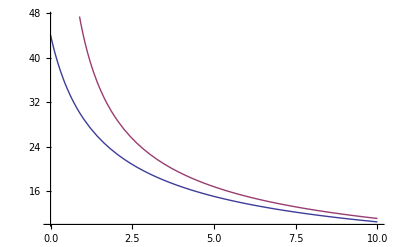

```mathematica
Plot[{((r + soft)/r0)^(-p),(r /r0)^(-p)},{r,0,10}]
```